# Data preprocessing for complex Wilson network

## 1410.2546

Data columns are: “r [fm]” “ReV/ImV [GeV]” “Err[ReV] [GeV]”

## 1607.04049

Data columns are:
“T [GeV]”
“r [fm]”
“Re[V] [GeV]” or “Im[V] [GeV]”
“Err[Re[V]] [GeV]” or “Err[Im[V]] [GeV]” this is the ten-bin Jackknife error
“Err[Re[V]] [GeV]” or “Err[Im[V]] [GeV]” this is the “systematic errors”

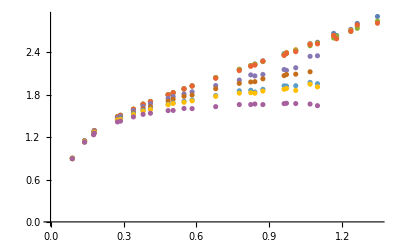

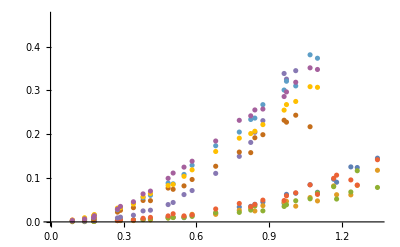

```mathematica
dataRe=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataRe,First]//ListPlot
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataIm,First]//ListPlot
```

Find the available temperatures.

```mathematica
temps=First/@dataRe//Union;
temps==Union[First/@dataIm]
```

True

Convert the data for each temperature to its own file in the correct format.

The target files have rows: “T r [1]”, “Re[V]/T [1]”, “Err[Re[V]]/T [1]”, “Im[V]/T [1]”, “Err[Im[V]]/T [1]”
Note: we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

T = 113 MeV

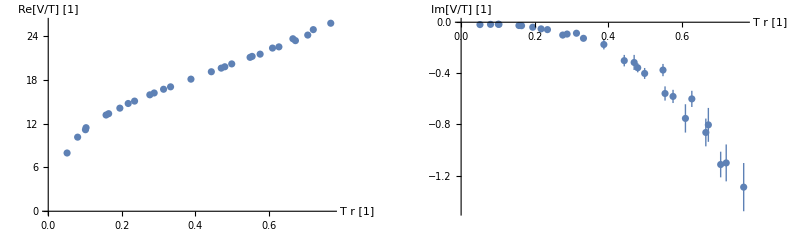

T = 226 MeV

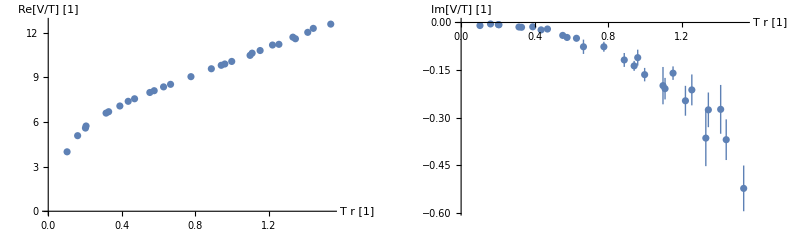

T = 254 MeV

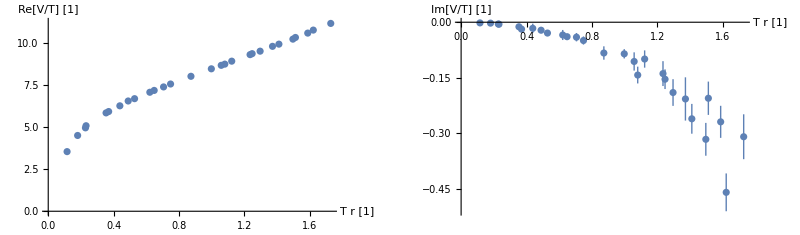

T = 271 MeV

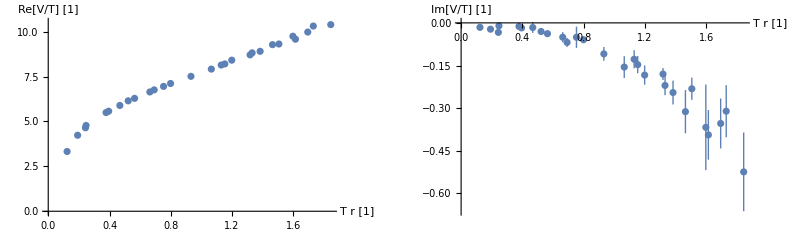

T = 290 MeV

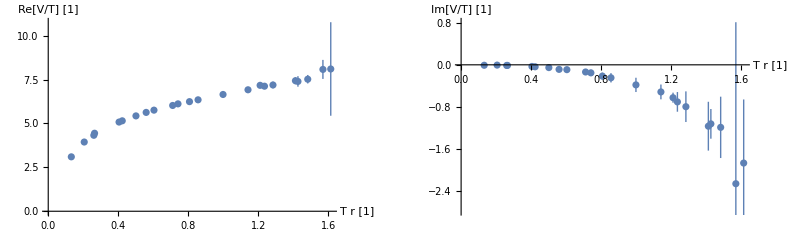

T = 312 MeV

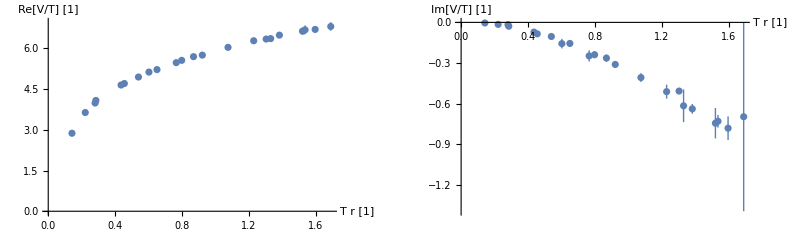

T = 338 MeV

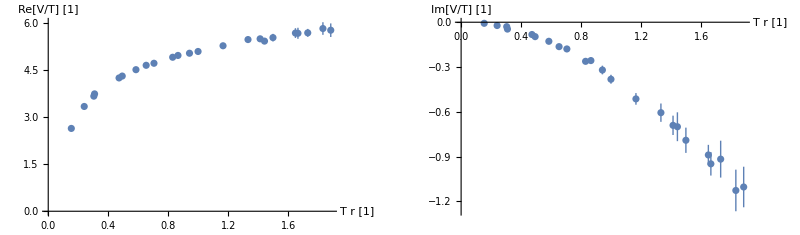

T = 369 MeV

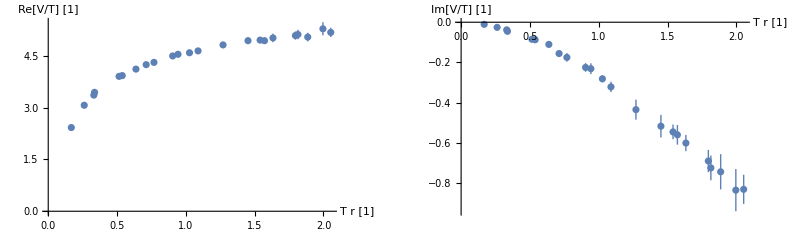

T = 406 MeV

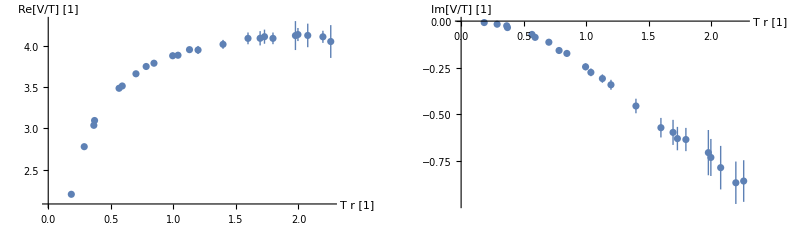

```mathematica
Block[{r,ReV,ReVσ,ImV,ImVσ,re,im},
Do[
re=Rest/@Select[dataRe,First[#]==T&];
im=Rest/@Select[dataIm,First[#]==T&];
Check[re⟦;;,1⟧==im⟦;;,1⟧,"Inconsistent widths in Re and Im files."];
r=re⟦;;,1⟧;
ReV=re⟦;;,2⟧;
ReVσ=re⟦;;,3⟧;
ImV=im⟦;;,2⟧;
ImVσ=im⟦;;,3⟧;
Print["T = "<>ToString[Round[1000T]]<>" MeV"];
GraphicsRow[{ListPlot[Thread@{T fmToInvGeV[r],Around@@@Thread[{ReV/T,ReVσ/T}]},AxesLabel->{"T r [1]","Re[V/T] [1]"}],ListPlot[Thread@{T fmToInvGeV[r],Around@@@Thread[{-ImV/T,ImVσ/T}]},AxesLabel->{"T r [1]","Im[V/T] [1]"}]}]//Print;
Export[NotebookDirectory[]<>"data/preprocessed/1607.04049/"<>ToString[Round[1000T]]<>"MeV.txt",{T fmToInvGeV[r],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"],
{T,temps}
]
]
```

Note that these plot don’t have the manual shifts that Fig. 2 has.

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.